```mathematica
zres = 1/(1/r+I*ω c-I/(ω l));
zresg = -I*zr*Cot[ω/ω0*π];
zin = -I/(ω cin);
```

```mathematica
ztotg=zresg+zin;
ztot=zres+zin;
```

```mathematica
s11n = FullSimplify[(zres-z0)/(zres+z0)];
s11 = FullSimplify[(ztot-z0)/(ztot+z0)];
s11g = FullSimplify[(ztotg-z0)/(ztotg+z0)];
```

```mathematica
wp = {c->π/2,l->2/π,r->10000000000,cin->0.1,z0->1,zr->1,ω0->1}
```

{c→π/2,l→2/π,r→10000000000,cin→0.1,z0→1,zr→1,ω0→1}

```mathematica
Abs[zresg] /.wp /.{ω->1.2}
```

1.37638

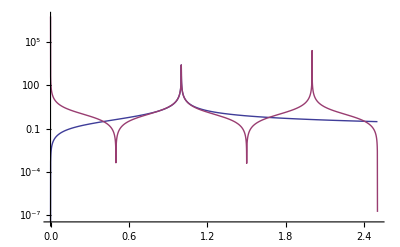

```mathematica
LogPlot[{Abs[zres] /.wp,Abs[zresg] /.wp},{ω,0,2.5},PlotRange->Full]
```

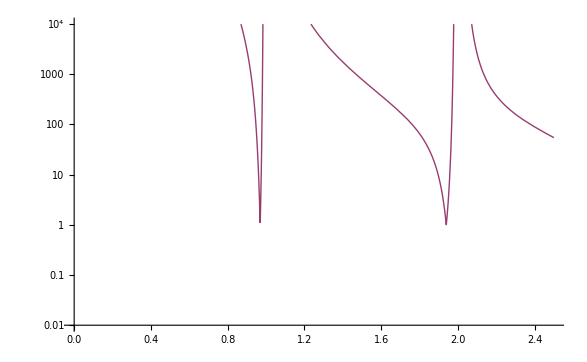

```mathematica
LogPlot[{Abs[ztot]/. wp,Abs[ztotg]/. wp} ,{ω,0.,2.5},PlotRange->{0.01,1*^4}]
```

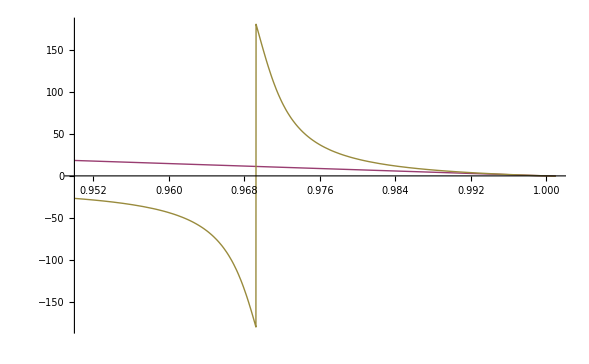

```mathematica
Plot[{Arg[s11]*180/π/. wp,Arg[s11n]*180/π/. wp,Arg[s11g]*180/π/. wp} ,{ω,0.95,1.001},PlotRange->Full]
```

```mathematica
zabsdata=Map[Block[{ω=#},{ω,Abs[zres]/. wp /. {ω->ω},Abs[zresg]/. wp /.{ω->ω}}]&,Range[0.1,2.5,0.0005]];
ztotabsdata=Map[Block[{ω=#},{ω,Abs[ztot]/. wp /. {ω->ω},Abs[ztotg]/. wp /.{ω->ω}}]&,Range[0.1,2.5,0.0005]];
phasedata=Map[Block[{ω=#},{ω,Arg[s11]*180/π/. wp /.{ω->ω},Arg[s11g]*180/π/. wp /.{ω->ω}}]&,Range[0.1,2.5,0.0005]];
```

```mathematica
Export[NotebookDirectory[]<>"lcr_and_cpw_resonator_zabs.csv",zabsdata]
Export[NotebookDirectory[]<>"lcr_and_cpw_resonator_ztotabs.csv",ztotabsdata]
Export[NotebookDirectory[]<>"lcr_and_cpw_resonator_phase.csv",phasedata]
```

E:\cygwin\home\adewes\thesis\material\mathematica\lcr_and_cpw_resonator_zabs.csv

E:\cygwin\home\adewes\thesis\material\mathematica\lcr_and_cpw_resonator_ztotabs.csv

E:\cygwin\home\adewes\thesis\material\mathematica\lcr_and_cpw_resonator_phase.csv

```mathematica
ceff =c+cin*ω/((z0*ω*cin)^2+1);
```

```mathematica
ceff /. {ω->ω0}/. wp
```

1.66981

```mathematica
ωeff = 1/Sqrt[ceff*l]/. {ω->ω0}/. wp
```

0.9699

```mathematica
1/Sqrt[c*l] /. wp
```

1

```mathematica
Sqrt[1.5807]
```

1.25726